```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/zack/oscillators/faraday

```mathematica
g=980;
σ=72;
ρ=1;
k0=2*Pi/4*2.5;
h0=2.0;
M2=4;
κ[k_, n_]:=k+n*k0;
H1[k_,A_]:=Table[Exp[-κ[k,n]*h0]*(g+σ/ρ*κ[k,n]^2)*κ[k,n]*(BesselJ[m-n,-I*κ[k,n]*A]-I/2*k0*A*BesselJ[m-n-1,-I*κ[k,n]*A]-I/2*k0*A*BesselJ[m-n+1,-I*κ[k,n]*A])-Exp[κ[k,n]*h0]*(g+σ/ρ*κ[k,n]^2)*κ[k,n]*(BesselJ[m-n,I*κ[k,n]*A]+I/2*k0*A*BesselJ[m-n-1,I*κ[k,n]*A]+I/2*k0*A*BesselJ[m-n+1,I*κ[k,n]*A]),{n,-M2,M2},{m,-M2,M2}];
H2[k_,A_]:=-Table[Exp[-κ[k,n]*h0]*(BesselJ[m-n,-I*κ[k,n]*A]-I/2*k0*A*BesselJ[m-n-1,-I*κ[k,n]*A]-I/2*k0*A*BesselJ[m-n+1,-I*κ[k,n]*A])+Exp[κ[k,n]*h0]*(BesselJ[m-n,I*κ[k,n]*A]+I/2*k0*A*BesselJ[m-n-1,I*κ[k,n]*A]+I/2*k0*A*BesselJ[m-n+1,I*κ[k,n]*A]),{n,-M2,M2},{m,-M2,M2}];
H3[k_,A_]:=Table[1.0/Cosh[κ[k,n]*h0]*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2}];
sys[k_,A_]:={H3[k,A].H1[k,A],H3[k,A].H2[k,A]};
```

```mathematica
AbsoluteTiming[Monitor[homogeneous=Transpose[Table[{k,#^(1/2)/(2*Pi)}&/@(SingularValueList[sys[k,0.0]][[-3;;-1]]),{k,-k0/2+0.01,k0/2-0.01,k0/200}]];,k/k0]]
AbsoluteTiming[Monitor[inhomogeneous=Transpose[Table[{k,#^(1/2)/(2*Pi)-0.25}&/@SingularValueList[sys[k,1.75]][[-3;;-1]],{k,-k0/2+0.01,k0/2-0.01,k0/200}]];,k/k0]]
```

{0.667589,Null}

{3.77382,Null}

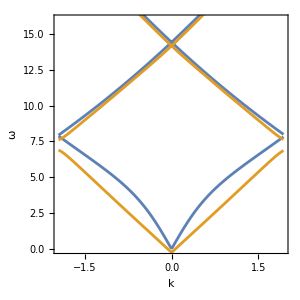

inviscidgap.pdf

```mathematica
p1=ListPlot[homogeneous,Joined->True,Axes->False,Frame->True,FrameLabel->{k,ω},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ImageSize->300,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[1]]]];
p2=ListPlot[inhomogeneous,Joined->True,Axes->False,Frame->True,FrameLabel->{k,ω},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ImageSize->300,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[2]]]];
p=Show[{{p1,p2}},PlotRange->{0,16}]
Export["inviscidgap.pdf",p]
```

```mathematica
Export["inviscidgap.dat",inhomogeneous, "CSV"]
```

inviscidgap.dat